## Setup

#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell"]["WolframInstitute`Infrageometry`",FileNameJoin[{NotebookDirectory[],"..","Infrageometry"}]]
```

## Playground

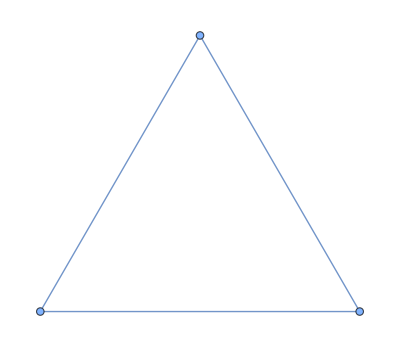
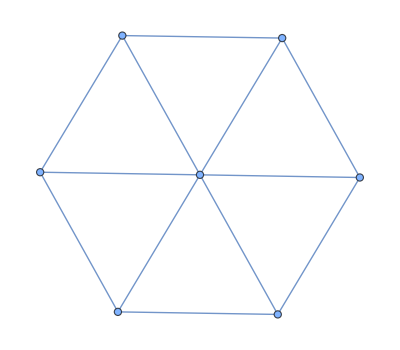
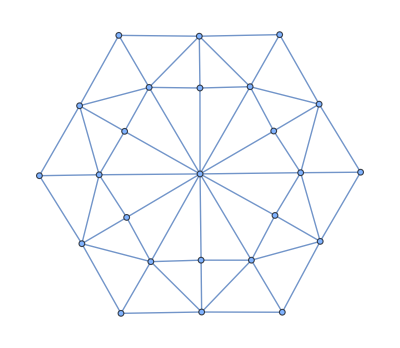
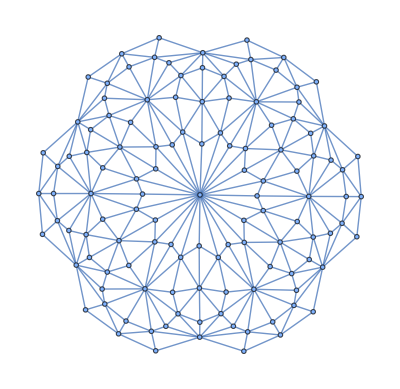
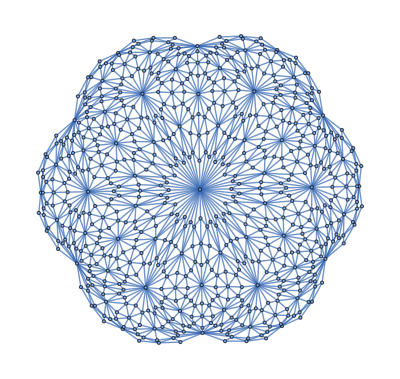

```mathematica
NestList[BarycentricRefinement,CycleGraph[3],4]
```

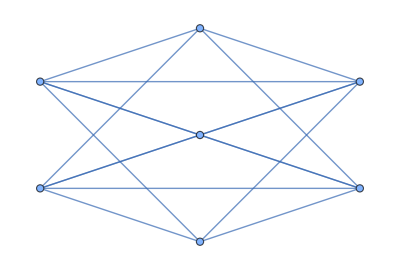

{{1},{2},{3},{4},{5},{6},{7},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{2,6},{2,7},{3,6},{3,7},{4,6},{4,7},{5,6},{5,7},{1,3,6},{1,3,7},{1,4,6},{1,4,7},{1,5,6},{1,5,7},{2,3,6},{2,3,7},{2,4,6},{2,4,7},{2,5,6},{2,5,7}}

```mathematica
t=CompleteGraph[{2,3,2}]
G=GraphComplex[t]
```

```mathematica
With[{l=ConnectionMatrix[G,#],g=GreenFunctionMatrix[G,#]},
{
Inverse[l]==Transpose[g],
Total[Flatten[g]]==ComplexEulerCharacteristic[G],
Det[l]==ComplexFermiCharacteristic[G],
Total[Sign[N[Eigenvalues[l]]]]==ComplexEulerCharacteristic[G]
}
]&/@RandomGraphAutomorphism[t,All]
```

{{True,True,False,False},{True,True,True,True},{True,True,False,False},{True,True,True,False},{True,True,True,False},{True,True,True,False},{True,True,False,False},{True,True,True,False},{True,True,True,False},{True,True,True,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,True,True},{True,True,False,False},{True,True,True,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,True,False},{True,True,True,False},{True,True,False,False},{True,True,True,False},{True,True,False,False},{True,True,True,False},{True,True,False,False},{True,True,False,False},{True,True,True,False},{True,True,False,False},{True,True,False,False},{True,True,True,False},{True,True,True,True},{True,True,True,False},{True,True,True,False},{True,True,True,False},{True,True,True,False},{True,True,False,False},{True,True,True,False},{True,True,True,True},{True,True,False,False},{True,True,True,False},{True,True,True,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,False,False},{True,True,False,False}}